```mathematica
Tt = 1/a ArcTanh[t/x];
Xt =√(x^2-t^2);
```

```mathematica
first = T ==Tt;
second = X==Xt;
```

```mathematica
trans = FullSimplify[Solve[first && second, {x,t}],Assumptions->  T ∈ Reals && X∈ Reals && a ∈ Reals]
```

{{x→-X Cosh[a T],t→-X Sinh[a T]},{x→X Cosh[a T],t→X Sinh[a T]}}

```mathematica
xt= FullSimplify[trans[[2,1,2]],Assumptions->a ∈ Reals && t ∈ Reals && x∈ Reals]
tt = FullSimplify[trans[[2,2,2]],Assumptions->a ∈ Reals && t ∈ Reals && x∈ Reals]
```

X Cosh[a T]

X Sinh[a T]

```mathematica
dT = FullSimplify[{D[Tt,t] , D[Tt,x]}]
dX =FullSimplify[{ D[Xt,t],D[Xt,x] }]
```

{x/(a (-t^2+x^2)),t/(a t^2-a x^2)}

{-t/(√(-t^2+x^2)),x/(√(-t^2+x^2))}

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

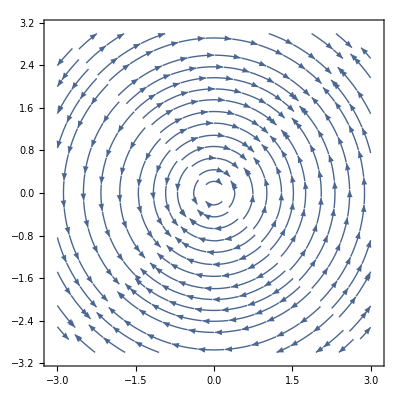

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

StreamPlot[{dX⟦2⟧,dX⟦1⟧}/.a→1,{x,-3,3},{t,-3,3}]

```mathematica
StreamPlot[{dT[[2]],dT[[1]]}/. a-> 1,{x,-3,3},{t,-3,3}]
StreamPlot[{dX[[2]],dX[[1]]}/. a-> 1,{x,-3,3},{t,-3,3}]
```

```mathematica
eT = FullSimplify[{D[tt,T] , D[xt,T]}]
eX = FullSimplify[{ D[tt,X],D[xt,X]}]
```

{a X Cosh[a T],a X Sinh[a T]}

{Sinh[a T],Cosh[a T]}

```mathematica
StreamPlot[{eT[[2]],eT[[1]]}/. a-> 1,{x,0.01,3},{t,0.01,3}];
StreamPlot[{eX[[2]],eX[[1]]}/. a-> 1,{x,0.01,3},{t,0.01,3}];
```

#### Part b.

```mathematica
η={{-1,0},{0,1}}
```

{{-1,0},{0,1}}

```mathematica
(g=FullSimplify[{{eT.η.eT,eT.η.eX},{eX.η.eT, eX.η.eX}}]  //FullSimplify) //MatrixForm
```

(-a^2 X^2 | 0
0 | 1)

```mathematica
(gInv={{dT.η.dT,dT.η.dX},{dX.η.dT, dX.η.dX}}  //FullSimplify) //MatrixForm
```

(1/(a^2 (t^2-x^2)) | 0
0 | 1)

```mathematica
g.gInv //FullSimplify
```

{{-X^2/(t^2-x^2),0},{0,1}}

```mathematica
dg = {D[g,T],D[g,X]} //FullSimplify
```

{{{0,0},{0,0}},{{-2 a^2 X,0},{0,0}}}

```mathematica
Γ[γ_,β_,μ_] = 1/2((gInv[[1,γ]]dg[[μ,1,β]]+gInv[[1,γ]]dg[[β,1,μ]]-gInv[[1,γ]] dg[[1,β,μ]]) + (gInv[[2,γ]]dg[[μ,2,β]]+gInv[[2,γ]]dg[[β,2,μ]]-gInv[[2,γ]] dg[[2,β,μ]])) //FullSimplify;
```

Part::pkspec1: The expression γ cannot be used as a part specification.

Part::pkspec1: The expression μ cannot be used as a part specification.

Part::pkspec1: The expression γ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

```mathematica
Γ[1,1,1] //FullSimplify
```

0

```mathematica
Γ[1,1,2] //Expand//FullSimplify
```

-X/(t^2-x^2)

```mathematica
Γ[1,2,1] //Expand//FullSimplify
```

-X/(t^2-x^2)

```mathematica
Γ[1,2,2] //Expand//FullSimplify
```

0

```mathematica
Γ[2,1,1] //Expand//FullSimplify
```

a^2 X

```mathematica
Γ[2,1,2] //FullSimplify
```

0

```mathematica
Γ[2,2,1] //Expand//FullSimplify
```

0

```mathematica
Γ[2,2,2] //Expand//FullSimplify
```

0